```mathematica
EOS-QCD- massa do S
```

EOS-QCD-do massa S

```mathematica
Clear["Global`*"]


fm= (5.07*10^(-3));  (*conversao de MeV para fm-1*)

(*____________________MASSAS_________________________*)
me= 0.5*fm;     (*em MeV convertido em fm-1*)
mu = 5*fm;         (*em MeV convertido em fm-1*)
md= 7*fm;                       (*em MeV convertido em fm-1*)
ms=150*fm;                  (*em MeV convertido em fm-1*)

(*__________________________________________________*)
gammaq = 6;
gammae=2;
media=8;
B =75.7; (* MeV/fm3*)
gh =mg*0.000657; 


fator1 = 1/((5.07*10^(-3))^(3));
fator2= 1/(5.07*10^(-3));

Print[" 1 MeV/fm3 = 1.7824*10^(12) g/cm3"]
```

1 MeV/fm3 = 1.7824*10^(12) g/cm3

```mathematica
(*Pressao - QCD*)

pq= (1/3)*(gammaq/(2*Pi*Pi))* fator2*( ((x^3)*(x^2 + mu^2)^(1/2))/4 -3* (mu*mu*x*(x^2 + mu^2)^(1/2))/8   +3* ((mu^4)*Log[x + (x^2 + mu^2)^(1/2)])/8 -  3*(mu^4) *Log[mu^2]/16 )+

  (1/3)* (gammaq/(2*Pi*Pi))* fator2*(((y^3)*(y^2 + md^2)^(1/2))/4   -3* (md*md*y*(y^2 + md^2)^(1/2))/8   +3* ((md^4)*Log[y + (y^2 + md^2)^(1/2)])/8 -  3*(md^4) *Log[md^2]/16 )+

  (1/3)* (gammaq/(2*Pi*Pi))* fator2*(((z^3)*(z^2 + ms^2)^(1/2))/4   -3* (ms*ms*z*(z^2 + ms^2)^(1/2))/8   +3* ((ms^4)*Log[z + (z^2 + ms^2)^(1/2)])/8 -  3*(ms^4) *Log[ms^2]/16 );

pe = (gammae/ (2*Pi*Pi))* fator2*(  ((w^3)*(w^2 + me^2)^(1/2))/4   -3* (me*me*w*(w^2 + me^2)^(1/2))/8   +3* ((me^4)*Log[w + (w^2 + me^2)^(1/2)])/8 -  3*(me^4)* Log[me^2]/16 );

(*fermions da pressão:*)
fermip=pq+pe;
(*expressão da pressão:*)
pressao= (27/(2*media))* fator1*((gh*gh)/(mg*mg))*rho*rho - B + pq + pe;

(*Densidade de Energia - QCD *)


eq=    
(1/3)*(3*gammaq/ (2*Pi*Pi))*fator2* (  ( (x^3)*(x^2 + mu^2)^(1/2))/4   + (mu*mu*x*(x^2 + mu^2)^(1/2))/8   - ( (mu^4)*Log[x + (x^2 + mu^2)^(1/2)])/8 +  (mu^4) *Log[mu^2]/16 )+

(1/3)*(3*gammaq/(2*Pi*Pi))*fator2*(( (y^3)*(y^2 + md^2)^(1/2))/4  + (md*md*y*(y^2 + md^2)^(1/2))/8   - ( (md^4)*Log[y + (y^2 + md^2)^(1/2)])/8 + (md^4)* Log[md^2]/16 )+

(1/3)*(3*gammaq/(2*Pi*Pi))*fator2*( ( (z^3)*(z^2 + ms^2)^(1/2))/4   + (ms*ms*z*(z^2 + ms^2)^(1/2))/8   - ( (ms^4)*Log[z + (z^2 + ms^2)^(1/2)])/8 +(ms^4) *Log[ms^2]/16 );

ee=(gammae/ (2*Pi*Pi))*fator2* (   ( (w^3)*(w^2 + me^2)^(1/2))/4   + (me*me*w*(w^2 + me^2)^(1/2))/8   - ( (me^4)*Log[w + (w^2 + me^2)^(1/2)])/8 +(me^4) *Log[me^2]/16 );

(*fermions da densidade de energia:*)
fermie=eq+ee;
(*expressão da densidade de energia:*)
energia = (27/(2*media))* fator1*((gh*gh)/(mg*mg))*rho*rho + B + eq+ee;

(*termo dos hardgluons -- comun para densidade de energia e pressão:*)
hardgluons=(27/(2*media))* fator1*((gh*gh)/(mg*mg))*rho*rho
```

5.58921 rho^2

```mathematica
(* Pressao - MIT *)
pressaomit = -B + pq+pe;


(* Densidade de Energia - MIT *)


energiamit =B + eq+ee;


(* Velocidade do som^2- MIT *)

csoq=pressaomit/energiamit;

(* Potencial barioquimico *)

muB = (energia+ pressao)/rho;
```

```mathematica
(*Cálculo do MOMENTOS DE FERMI DAS PARTÍCULAS: u,d,s,e*)

lista = {};
Do[    {rho=j,(*inicio do DO*)

sol = NSolve[{ku^3+ kd^3+ ks^3 == 3* Pi*Pi* rho, 2*ku^3 ==  kd^3 + ks^3 + ke^3, kd^2 + md^2 == ks^2 + ms^2, (ku^2 + mu^2)^(1/2)  + (ke^2 + me^2)^(1/2) == (ks^2 + ms^2)^(1/2)},{ku,kd,ks,ke}];

 k1= Re[ ku/.sol]; k2= Re[ kd/.sol]; k3= Re[ ks/.sol]; k4= Re[ ke/.sol];

              For[i=1,i≤ 28,                              (*inicio do FOR*)

                                                         If[                                     k1[[i]]> 0, 
                                                       If[                              k2[[i]]>0, 
                                                    If[                        k3[[i]]>0,
                                                  If[                k4[[i]]>0,
      
                   x =   k1[[i]];
                   y=    k2[[i]];
                   z =   k3[[i]];
                   w=    k4[[i]]      ]    ]   ]   ];    
        i++],                                                        (*fim do FOR*)

(*--------------------------------------------------------*)
energia;   

     pressao;

energiamit;

pressaomit;

muB;

(*--------------------------------------------------------*)

             lista = Append[lista, { rho,x,y,z,w, energia, pressao, energiamit, pressaomit, (pressao/pressaomit), fermie, fermip,hardgluons, muB}];  },
 
{j,0.10,4.5,0.01 } ];(*fim do DO*)
```

```mathematica
listapressaorho={};
Do[listapressaorho=Append[listapressaorho,{lista[[i,1]],lista[[i,7]]}],{i,(4.5- 0.10)/0.01}]
listapressaorho; 

listapressaomitrho={};
Do[listapressaomitrho=Append[listapressaomitrho,{lista[[i,1]],lista[[i,9]]}],{i,(4.5- 0.10)/0.01}]
listapressaomitrho; 

 (*Grafico da pressao versus rho - QCD*)
G1=ListPlot[listapressaorho,PlotJoined->True,PlotStyle-> {Blue},PlotRange->{{0,5},{0,8000}}
,AxesLabel->{"rho","pressao"},PlotStyle->{Blue}];

(*Grafico da pressao versus rho - MIT*)
G2=ListPlot[listapressaomitrho,PlotJoined->True,PlotStyle-> {Red},PlotRange->{{0,5},{0,8000}}
,AxesLabel->{"rho","pressao"},PlotStyle->{Blue}];

Show[G1,G2]
```

ListPlot::optx: Unknown option PlotJoined → True in ListPlot[{{0.1, -61.3373}, {0.11, -59.4516}, {0.12, -57.503}, {0.13, -55.4948}, {0.14, -53.4299}, {0.15, -51.3108}, {0.16, -49.1399}, {0.17, -46.9193}, « 36 », {0.54, 60.3189}, {0.55, 63.7411}, {0.56, 67.1858}, {0.57, 70.6528}, {0.58, 74.1418}, {0.59, 77.6526}, « 390 »}, « 4 », PlotStyle → {« 1 »}].

ListPlot::optx: Unknown option PlotJoined → True in ListPlot[{{0.1, -61.3932}, {0.11, -59.5192}, {0.12, -57.5835}, {0.13, -55.5892}, {0.14, -53.5394}, {0.15, -51.4366}, {0.16, -49.283}, {0.17, -47.0808}, « 36 », {0.54, 58.6891}, {0.55, 62.0503}, {0.56, 65.433}, {0.57, 68.8368}, {0.58, 72.2616}, {0.59, 75.707}, « 390 »}, « 4 », PlotStyle → « 1 »].

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[{{0.1, -61.3373}, {0.11, -59.4516}, {0.12, -57.503}, {0.13, -55.4948}, {0.14, -53.4299}, {0.15, -51.3108}, {0.16, -49.1399}, « 37 », {0.54, 60.3189}, {0.55, 63.7411}, {0.56, 67.1858}, {0.57, 70.6528}, {0.58, 74.1418}, {0.59, 77.6526}, « 390 »}, « 4 », PlotStyle → {RGBColor[0, 0, 1]}], « 1 »].

Show[ListPlot[{{0.1,-61.3373},{0.11,-59.4516},{0.12,-57.503},{0.13,-55.4948},{0.14,-53.4299},{0.15,-51.3108},{0.16,-49.1399},{0.17,-46.9193},{0.18,-44.6507},{0.19,-42.3359},{0.2,-39.9765},{0.21,-37.5739},{0.22,-35.1294},{0.23,-32.6443},{0.24,-30.1197},{0.25,-27.5568},{0.26,-24.9563},{0.27,-22.3194},{0.28,-19.6469},{0.29,-16.9396},{0.3,-14.1982},{0.31,-11.4236},{0.32,-8.61644},{0.33,-5.77733},{0.34,-2.90692},{0.35,-0.00581327},{0.36,2.92543},{0.37,5.88625},{0.38,8.87615},{0.39,11.8946},{0.4,14.9412},{0.41,18.0154},{0.42,21.1169},{0.43,24.2451},{0.44,27.3997},{0.45,30.5804},{0.46,33.7866},{0.47,37.0182},{0.48,40.2746},{0.49,43.5557},{0.5,46.861},{0.51,50.1903},{0.52,53.5432},{0.53,56.9195},{0.54,60.3189},{0.55,63.7411},{0.56,67.1858},{0.57,70.6528},{0.58,74.1418},{0.59,77.6526},{0.6,81.185},{0.61,84.7387},{0.62,88.3135},{0.63,91.9091},{0.64,95.5255},{0.65,99.1623},{0.66,102.819},{0.67,106.496},{0.68,110.193},{0.69,113.91},{0.7,117.646},{0.71,121.402},{0.72,125.177},{0.73,128.97},{0.74,132.783},{0.75,136.614},{0.76,140.463},{0.77,144.331},{0.78,148.218},{0.79,152.122},{0.8,156.044},{0.81,159.984},{0.82,163.941},{0.83,167.917},{0.84,171.909},{0.85,175.918},{0.86,179.945},{0.87,183.989},{0.88,188.049},{0.89,192.127},{0.9,196.22},{0.91,200.331},{0.92,204.458},{0.93,208.601},{0.94,212.76},{0.95,216.935},{0.96,221.126},{0.97,225.333},{0.98,229.556},{0.99,233.794},{1.,238.048},{1.01,242.317},{1.02,246.602},{1.03,250.902},{1.04,255.217},{1.05,259.547},{1.06,263.892},{1.07,268.252},{1.08,272.627},{1.09,277.017},{1.1,281.421},{1.11,285.84},{1.12,290.273},{1.13,294.721},{1.14,299.182},{1.15,303.659},{1.16,308.149},{1.17,312.653},{1.18,317.172},{1.19,321.704},{1.2,326.25},{1.21,330.81},{1.22,335.383},{1.23,339.971},{1.24,344.572},{1.25,349.186},{1.26,353.814},{1.27,358.455},{1.28,363.11},{1.29,367.777},{1.3,372.458},{1.31,377.152},{1.32,381.859},{1.33,386.579},{1.34,391.312},{1.35,396.058},{1.36,400.817},{1.37,405.589},{1.38,410.373},{1.39,415.17},{1.4,419.979},{1.41,424.801},{1.42,429.636},{1.43,434.482},{1.44,439.342},{1.45,444.213},{1.46,449.097},{1.47,453.993},{1.48,458.901},{1.49,463.822},{1.5,468.754},{1.51,473.699},{1.52,478.655},{1.53,483.623},{1.54,488.604},{1.55,493.596},{1.56,498.599},{1.57,503.615},{1.58,508.642},{1.59,513.681},{1.6,518.732},{1.61,523.794},{1.62,528.867},{1.63,533.952},{1.64,539.049},{1.65,544.156},{1.66,549.276},{1.67,554.406},{1.68,559.548},{1.69,564.701},{1.7,569.865},{1.71,575.04},{1.72,580.226},{1.73,585.424},{1.74,590.632},{1.75,595.852},{1.76,601.082},{1.77,606.323},{1.78,611.575},{1.79,616.838},{1.8,622.112},{1.81,627.397},{1.82,632.692},{1.83,637.998},{1.84,643.314},{1.85,648.642},{1.86,653.979},{1.87,659.328},{1.88,664.687},{1.89,670.056},{1.9,675.436},{1.91,680.826},{1.92,686.226},{1.93,691.637},{1.94,697.059},{1.95,702.49},{1.96,707.932},{1.97,713.384},{1.98,718.846},{1.99,724.319},{2.,729.801},{2.01,735.294},{2.02,740.796},{2.03,746.309},{2.04,751.832},{2.05,757.364},{2.06,762.907},{2.07,768.46},{2.08,774.022},{2.09,779.594},{2.1,785.176},{2.11,790.768},{2.12,796.37},{2.13,801.982},{2.14,807.603},{2.15,813.234},{2.16,818.875},{2.17,824.525},{2.18,830.185},{2.19,835.854},{2.2,841.533},{2.21,847.222},{2.22,852.92},{2.23,858.627},{2.24,864.344},{2.25,870.071},{2.26,875.807},{2.27,881.552},{2.28,887.307},{2.29,893.071},{2.3,898.844},{2.31,904.627},{2.32,910.419},{2.33,916.22},{2.34,922.03},{2.35,927.85},{2.36,933.679},{2.37,939.516},{2.38,945.363},{2.39,951.22},{2.4,957.085},{2.41,962.959},{2.42,968.842},{2.43,974.735},{2.44,980.636},{2.45,986.546},{2.46,992.466},{2.47,998.394},{2.48,1004.33},{2.49,1010.28},{2.5,1016.23},{2.51,1022.2},{2.52,1028.17},{2.53,1034.15},{2.54,1040.14},{2.55,1046.14},{2.56,1052.15},{2.57,1058.16},{2.58,1064.19},{2.59,1070.22},{2.6,1076.26},{2.61,1082.32},{2.62,1088.37},{2.63,1094.44},{2.64,1100.52},{2.65,1106.61},{2.66,1112.7},{2.67,1118.8},{2.68,1124.91},{2.69,1131.03},{2.7,1137.16},{2.71,1143.3},{2.72,1149.44},{2.73,1155.6},{2.74,1161.76},{2.75,1167.93},{2.76,1174.11},{2.77,1180.29},{2.78,1186.49},{2.79,1192.69},{2.8,1198.9},{2.81,1205.12},{2.82,1211.35},{2.83,1217.59},{2.84,1223.83},{2.85,1230.09},{2.86,1236.35},{2.87,1242.62},{2.88,1248.9},{2.89,1255.18},{2.9,1261.48},{2.91,1267.78},{2.92,1274.09},{2.93,1280.41},{2.94,1286.73},{2.95,1293.07},{2.96,1299.41},{2.97,1305.76},{2.98,1312.12},{2.99,1318.48},{3.,1324.86},{3.01,1331.24},{3.02,1337.63},{3.03,1344.03},{3.04,1350.43},{3.05,1356.85},{3.06,1363.27},{3.07,1369.7},{3.08,1376.14},{3.09,1382.58},{3.1,1389.04},{3.11,1395.5},{3.12,1401.97},{3.13,1408.44},{3.14,1414.93},{3.15,1421.42},{3.16,1427.92},{3.17,1434.43},{3.18,1440.94},{3.19,1447.47},{3.2,1454.},{3.21,1460.53},{3.22,1467.08},{3.23,1473.63},{3.24,1480.2},{3.25,1486.76},{3.26,1493.34},{3.27,1499.92},{3.28,1506.52},{3.29,1513.12},{3.3,1519.72},{3.31,1526.34},{3.32,1532.96},{3.33,1539.59},{3.34,1546.22},{3.35,1552.87},{3.36,1559.52},{3.37,1566.18},{3.38,1572.85},{3.39,1579.52},{3.4,1586.2},{3.41,1592.89},{3.42,1599.59},{3.43,1606.29},{3.44,1613.},{3.45,1619.72},{3.46,1626.45},{3.47,1633.18},{3.48,1639.92},{3.49,1646.67},{3.5,1653.42},{3.51,1660.18},{3.52,1666.95},{3.53,1673.73},{3.54,1680.51},{3.55,1687.31},{3.56,1694.1},{3.57,1700.91},{3.58,1707.72},{3.59,1714.54},{3.6,1721.37},{3.61,1728.21},{3.62,1735.05},{3.63,1741.9},{3.64,1748.75},{3.65,1755.61},{3.66,1762.48},{3.67,1769.36},{3.68,1776.25},{3.69,1783.14},{3.7,1790.04},{3.71,1796.94},{3.72,1803.85},{3.73,1810.77},{3.74,1817.7},{3.75,1824.63},{3.76,1831.58},{3.77,1838.52},{3.78,1845.48},{3.79,1852.44},{3.8,1859.41},{3.81,1866.38},{3.82,1873.37},{3.83,1880.36},{3.84,1887.35},{3.85,1894.36},{3.86,1901.37},{3.87,1908.38},{3.88,1915.41},{3.89,1922.44},{3.9,1929.48},{3.91,1936.52},{3.92,1943.57},{3.93,1950.63},{3.94,1957.69},{3.95,1964.77},{3.96,1971.85},{3.97,1978.93},{3.98,1986.02},{3.99,1993.12},{4.,2000.23},{4.01,2007.34},{4.02,2014.46},{4.03,2021.59},{4.04,2028.72},{4.05,2035.86},{4.06,2043.},{4.07,2050.16},{4.08,2057.32},{4.09,2064.48},{4.1,2071.66},{4.11,2078.84},{4.12,2086.02},{4.13,2093.21},{4.14,2100.41},{4.15,2107.62},{4.16,2114.83},{4.17,2122.05},{4.18,2129.28},{4.19,2136.51},{4.2,2143.75},{4.21,2151.},{4.22,2158.25},{4.23,2165.51},{4.24,2172.77},{4.25,2180.04},{4.26,2187.32},{4.27,2194.61},{4.28,2201.9},{4.29,2209.2},{4.3,2216.5},{4.31,2223.81},{4.32,2231.13},{4.33,2238.45},{4.34,2245.79},{4.35,2253.12},{4.36,2260.47},{4.37,2267.82},{4.38,2275.17},{4.39,2282.53},{4.4,2289.9},{4.41,2297.28},{4.42,2304.66},{4.43,2312.05},{4.44,2319.44},{4.45,2326.84},{4.46,2334.25},{4.47,2341.67},{4.48,2349.09},{4.49,2356.51}},PlotJoined→True,PlotStyle→{RGBColor[0,0,1]},PlotRange→{{0,5},{0,8000}},AxesLabel→{rho,pressao},PlotStyle→{RGBColor[0,0,1]}],ListPlot[{{0.1,-61.3932},{0.11,-59.5192},{0.12,-57.5835},{0.13,-55.5892},{0.14,-53.5394},{0.15,-51.4366},{0.16,-49.283},{0.17,-47.0808},{0.18,-44.8318},{0.19,-42.5377},{0.2,-40.2},{0.21,-37.8204},{0.22,-35.3999},{0.23,-32.94},{0.24,-30.4417},{0.25,-27.9061},{0.26,-25.3342},{0.27,-22.7269},{0.28,-20.0851},{0.29,-17.4096},{0.3,-14.7013},{0.31,-11.9608},{0.32,-9.18878},{0.33,-6.386},{0.34,-3.55303},{0.35,-0.690492},{0.36,2.20106},{0.37,5.12109},{0.38,8.06907},{0.39,11.0445},{0.4,14.0469},{0.41,17.0759},{0.42,20.1309},{0.43,23.2117},{0.44,26.3177},{0.45,29.4485},{0.46,32.6039},{0.47,35.7835},{0.48,38.9869},{0.49,42.2137},{0.5,45.4637},{0.51,48.7365},{0.52,52.0319},{0.53,55.3495},{0.54,58.6891},{0.55,62.0503},{0.56,65.433},{0.57,68.8368},{0.58,72.2616},{0.59,75.707},{0.6,79.1729},{0.61,82.6589},{0.62,86.165},{0.63,89.6908},{0.64,93.2361},{0.65,96.8008},{0.66,100.385},{0.67,103.987},{0.68,107.609},{0.69,111.249},{0.7,114.908},{0.71,118.584},{0.72,122.279},{0.73,125.992},{0.74,129.722},{0.75,133.47},{0.76,137.235},{0.77,141.018},{0.78,144.817},{0.79,148.634},{0.8,152.467},{0.81,156.317},{0.82,160.183},{0.83,164.066},{0.84,167.965},{0.85,171.88},{0.86,175.811},{0.87,179.758},{0.88,183.721},{0.89,187.699},{0.9,191.693},{0.91,195.702},{0.92,199.727},{0.93,203.766},{0.94,207.821},{0.95,211.891},{0.96,215.975},{0.97,220.074},{0.98,224.188},{0.99,228.316},{1.,232.459},{1.01,236.616},{1.02,240.787},{1.03,244.972},{1.04,249.172},{1.05,253.385},{1.06,257.612},{1.07,261.853},{1.08,266.108},{1.09,270.376},{1.1,274.658},{1.11,278.953},{1.12,283.262},{1.13,287.584},{1.14,291.919},{1.15,296.267},{1.16,300.628},{1.17,305.002},{1.18,309.389},{1.19,313.789},{1.2,318.201},{1.21,322.627},{1.22,327.065},{1.23,331.515},{1.24,335.978},{1.25,340.453},{1.26,344.94},{1.27,349.44},{1.28,353.952},{1.29,358.476},{1.3,363.012},{1.31,367.561},{1.32,372.121},{1.33,376.693},{1.34,381.276},{1.35,385.872},{1.36,390.479},{1.37,395.098},{1.38,399.729},{1.39,404.371},{1.4,409.024},{1.41,413.689},{1.42,418.365},{1.43,423.053},{1.44,427.752},{1.45,432.462},{1.46,437.183},{1.47,441.916},{1.48,446.659},{1.49,451.413},{1.5,456.179},{1.51,460.955},{1.52,465.742},{1.53,470.54},{1.54,475.348},{1.55,480.168},{1.56,484.998},{1.57,489.838},{1.58,494.689},{1.59,499.551},{1.6,504.423},{1.61,509.306},{1.62,514.199},{1.63,519.102},{1.64,524.016},{1.65,528.94},{1.66,533.874},{1.67,538.818},{1.68,543.773},{1.69,548.737},{1.7,553.712},{1.71,558.697},{1.72,563.691},{1.73,568.696},{1.74,573.71},{1.75,578.735},{1.76,583.769},{1.77,588.813},{1.78,593.867},{1.79,598.93},{1.8,604.003},{1.81,609.086},{1.82,614.178},{1.83,619.28},{1.84,624.392},{1.85,629.513},{1.86,634.643},{1.87,639.783},{1.88,644.932},{1.89,650.091},{1.9,655.259},{1.91,660.436},{1.92,665.622},{1.93,670.818},{1.94,676.023},{1.95,681.237},{1.96,686.46},{1.97,691.693},{1.98,696.934},{1.99,702.185},{2.,707.444},{2.01,712.713},{2.02,717.99},{2.03,723.276},{2.04,728.572},{2.05,733.876},{2.06,739.189},{2.07,744.51},{2.08,749.841},{2.09,755.18},{2.1,760.528},{2.11,765.885},{2.12,771.25},{2.13,776.624},{2.14,782.007},{2.15,787.398},{2.16,792.797},{2.17,798.206},{2.18,803.622},{2.19,809.048},{2.2,814.481},{2.21,819.923},{2.22,825.374},{2.23,830.833},{2.24,836.3},{2.25,841.776},{2.26,847.259},{2.27,852.752},{2.28,858.252},{2.29,863.76},{2.3,869.277},{2.31,874.802},{2.32,880.335},{2.33,885.877},{2.34,891.426},{2.35,896.983},{2.36,902.549},{2.37,908.122},{2.38,913.704},{2.39,919.293},{2.4,924.891},{2.41,930.496},{2.42,936.11},{2.43,941.731},{2.44,947.36},{2.45,952.997},{2.46,958.642},{2.47,964.295},{2.48,969.955},{2.49,975.623},{2.5,981.299},{2.51,986.983},{2.52,992.674},{2.53,998.374},{2.54,1004.08},{2.55,1009.79},{2.56,1015.52},{2.57,1021.25},{2.58,1026.98},{2.59,1032.73},{2.6,1038.48},{2.61,1044.24},{2.62,1050.01},{2.63,1055.78},{2.64,1061.57},{2.65,1067.36},{2.66,1073.15},{2.67,1078.96},{2.68,1084.77},{2.69,1090.59},{2.7,1096.42},{2.71,1102.25},{2.72,1108.09},{2.73,1113.94},{2.74,1119.8},{2.75,1125.66},{2.76,1131.53},{2.77,1137.41},{2.78,1143.29},{2.79,1149.19},{2.8,1155.08},{2.81,1160.99},{2.82,1166.9},{2.83,1172.83},{2.84,1178.75},{2.85,1184.69},{2.86,1190.63},{2.87,1196.58},{2.88,1202.54},{2.89,1208.5},{2.9,1214.47},{2.91,1220.45},{2.92,1226.43},{2.93,1232.42},{2.94,1238.42},{2.95,1244.43},{2.96,1250.44},{2.97,1256.46},{2.98,1262.48},{2.99,1268.52},{3.,1274.55},{3.01,1280.6},{3.02,1286.65},{3.03,1292.71},{3.04,1298.78},{3.05,1304.85},{3.06,1310.94},{3.07,1317.02},{3.08,1323.12},{3.09,1329.22},{3.1,1335.32},{3.11,1341.44},{3.12,1347.56},{3.13,1353.69},{3.14,1359.82},{3.15,1365.96},{3.16,1372.11},{3.17,1378.26},{3.18,1384.42},{3.19,1390.59},{3.2,1396.76},{3.21,1402.94},{3.22,1409.13},{3.23,1415.32},{3.24,1421.52},{3.25,1427.73},{3.26,1433.94},{3.27,1440.16},{3.28,1446.39},{3.29,1452.62},{3.3,1458.86},{3.31,1465.1},{3.32,1471.35},{3.33,1477.61},{3.34,1483.87},{3.35,1490.14},{3.36,1496.42},{3.37,1502.7},{3.38,1508.99},{3.39,1515.29},{3.4,1521.59},{3.41,1527.9},{3.42,1534.21},{3.43,1540.53},{3.44,1546.86},{3.45,1553.19},{3.46,1559.53},{3.47,1565.88},{3.48,1572.23},{3.49,1578.59},{3.5,1584.95},{3.51,1591.32},{3.52,1597.7},{3.53,1604.08},{3.54,1610.47},{3.55,1616.87},{3.56,1623.27},{3.57,1629.68},{3.58,1636.09},{3.59,1642.51},{3.6,1648.93},{3.61,1655.37},{3.62,1661.8},{3.63,1668.25},{3.64,1674.7},{3.65,1681.15},{3.66,1687.61},{3.67,1694.08},{3.68,1700.56},{3.69,1707.03},{3.7,1713.52},{3.71,1720.01},{3.72,1726.51},{3.73,1733.01},{3.74,1739.52},{3.75,1746.04},{3.76,1752.56},{3.77,1759.08},{3.78,1765.62},{3.79,1772.16},{3.8,1778.7},{3.81,1785.25},{3.82,1791.81},{3.83,1798.37},{3.84,1804.94},{3.85,1811.51},{3.86,1818.09},{3.87,1824.67},{3.88,1831.26},{3.89,1837.86},{3.9,1844.46},{3.91,1851.07},{3.92,1857.69},{3.93,1864.3},{3.94,1870.93},{3.95,1877.56},{3.96,1884.2},{3.97,1890.84},{3.98,1897.49},{3.99,1904.14},{4.,1910.8},{4.01,1917.47},{4.02,1924.14},{4.03,1930.81},{4.04,1937.49},{4.05,1944.18},{4.06,1950.87},{4.07,1957.57},{4.08,1964.28},{4.09,1970.99},{4.1,1977.7},{4.11,1984.42},{4.12,1991.15},{4.13,1997.88},{4.14,2004.62},{4.15,2011.36},{4.16,2018.11},{4.17,2024.86},{4.18,2031.62},{4.19,2038.39},{4.2,2045.16},{4.21,2051.93},{4.22,2058.71},{4.23,2065.5},{4.24,2072.29},{4.25,2079.09},{4.26,2085.89},{4.27,2092.7},{4.28,2099.51},{4.29,2106.33},{4.3,2113.16},{4.31,2119.99},{4.32,2126.82},{4.33,2133.66},{4.34,2140.51},{4.35,2147.36},{4.36,2154.22},{4.37,2161.08},{4.38,2167.95},{4.39,2174.82},{4.4,2181.7},{4.41,2188.58},{4.42,2195.47},{4.43,2202.36},{4.44,2209.26},{4.45,2216.16},{4.46,2223.07},{4.47,2229.99},{4.48,2236.91},{4.49,2243.83}},PlotJoined→True,PlotStyle→{RGBColor[1,0,0]},PlotRange→{{0,5},{0,8000}},AxesLabel→{rho,pressao},PlotStyle→{RGBColor[0,0,1]}]]

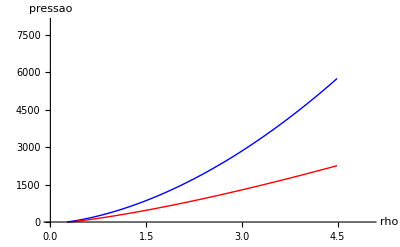

-Graphics-

```mathematica
Print["   rho       ku       kd       ks       ke           energiaQCD(MeV/fm3)        pressaoQCD(MeV/fm3)       energiaQCD/rho            razaoP "]
Print[" "]
Do[Print[PaddedForm[lista[[i,1]],{5,2}]," ",  PaddedForm[lista[[i,2]],{5,2} ],"  ",  PaddedForm[lista[[i,3]],{5,2}],"  ",  PaddedForm[lista[[i,4]],{5,2}], "   ",  PaddedForm[lista[[i,5]],{5,2}],  "               ",  PaddedForm[lista[[i,6]],{5,2}],  "                    ",  PaddedForm[lista[[i,7]],{5,2}],   "                      ",  PaddedForm[lista[[i,6]]/lista[[i,1]],{5,2}],   "             ", PaddedForm[lista[[i,10]],{5,1}]],{i,((4.5-0.10)/0.01) +1}];
```

rho       ku       kd       ks       ke           energiaQCD(MeV/fm3)        pressaoQCD(MeV/fm3)       energiaQCD/rho            razaoP

0.10    1.00     1.12     0.83      0.13                125.37                     -61.34                       1253.70                 1.0

0.11    1.03     1.15     0.86      0.12                131.86                     -59.45                       1198.70                 1.0

0.12    1.06     1.18     0.90      0.12                138.53                     -57.50                       1154.40                 1.0

0.13    1.09     1.20     0.93      0.12                145.36                     -55.49                       1118.20                 1.0

0.14    1.11     1.23     0.97      0.12                152.35                     -53.43                       1088.20                 1.0

0.15    1.14     1.25     1.00      0.11                159.49                     -51.31                       1063.30                 1.0

0.16    1.16     1.28     1.03      0.11                166.78                     -49.14                       1042.30                 1.0

0.17    1.19     1.30     1.05      0.11                174.20                     -46.92                       1024.70                 1.0

0.18    1.21     1.32     1.08      0.11                181.75                     -44.65                       1009.70                 1.0

0.19    1.23     1.34     1.10      0.11                189.43                     -42.34                       996.98                 1.0

0.20    1.25     1.36     1.13      0.11                197.23                     -39.98                       986.14                 1.0

0.21    1.28     1.38     1.15      0.10                205.15                     -37.57                       976.91                 1.0

0.22    1.29     1.40     1.17      0.10                213.19                     -35.13                       969.03                 1.0

0.23    1.31     1.42     1.19      0.10                221.34                     -32.64                       962.33                 1.0

0.24    1.33     1.43     1.22      0.10                229.59                     -30.12                       956.64                 1.0

0.25    1.35     1.45     1.24      0.10                237.96                     -27.56                       951.83                 1.0

0.26    1.37     1.47     1.25      0.10                246.43                     -24.96                       947.79                 1.0

0.27    1.39     1.48     1.27      0.10                254.99                     -22.32                       944.42                 1.0

0.28    1.40     1.50     1.29      0.10                263.66                     -19.65                       941.64                 1.0

0.29    1.42     1.51     1.31      0.09                272.42                     -16.94                       939.39                 1.0

0.30    1.44     1.53     1.33      0.09                281.28                     -14.20                       937.60                 1.0

0.31    1.45     1.54     1.34      0.09                290.23                     -11.42                       936.22                 1.0

0.32    1.47     1.56     1.36      0.09                299.27                      -8.62                       935.20                 0.9

0.33    1.48     1.57     1.38      0.09                308.39                      -5.78                       934.52                 0.9

0.34    1.50     1.59     1.39      0.09                317.61                      -2.91                       934.13                 0.8

0.35    1.51     1.60     1.41      0.09                326.90                      -0.01                       934.01                 0.0

0.36    1.53     1.61     1.43      0.09                336.28                       2.93                       934.12                 1.3

0.37    1.54     1.63     1.44      0.09                345.75                       5.89                       934.45                 1.1

0.38    1.55     1.64     1.45      0.09                355.29                       8.88                       934.98                 1.1

0.39    1.57     1.65     1.47      0.09                364.91                      11.89                       935.68                 1.1

0.40    1.58     1.67     1.48      0.09                374.61                      14.94                       936.54                 1.1

0.41    1.59     1.68     1.50      0.09                384.39                      18.02                       937.54                 1.1

0.42    1.61     1.69     1.51      0.09                394.24                      21.12                       938.68                 1.0

0.43    1.62     1.70     1.52      0.08                404.17                      24.25                       939.93                 1.0

0.44    1.63     1.72     1.54      0.08                414.17                      27.40                       941.29                 1.0

0.45    1.64     1.73     1.55      0.08                424.24                      30.58                       942.76                 1.0

0.46    1.66     1.74     1.56      0.08                434.38                      33.79                       944.31                 1.0

0.47    1.67     1.75     1.58      0.08                444.60                      37.02                       945.95                 1.0

0.48    1.68     1.76     1.59      0.08                454.88                      40.27                       947.66                 1.0

0.49    1.69     1.77     1.60      0.08                465.23                      43.56                       949.44                 1.0

0.50    1.70     1.78     1.61      0.08                475.64                      46.86                       951.29                 1.0

0.51    1.71     1.79     1.63      0.08                486.13                      50.19                       953.19                 1.0

0.52    1.72     1.80     1.64      0.08                496.68                      53.54                       955.15                 1.0

0.53    1.74     1.82     1.65      0.08                507.29                      56.92                       957.15                 1.0

0.54    1.75     1.83     1.66      0.08                517.97                      60.32                       959.20                 1.0

0.55    1.76     1.84     1.67      0.08                528.71                      63.74                       961.28                 1.0

0.56    1.77     1.85     1.68      0.08                539.51                      67.19                       963.41                 1.0

0.57    1.78     1.86     1.69      0.08                550.37                      70.65                       965.57                 1.0

0.58    1.79     1.87     1.70      0.08                561.30                      74.14                       967.76                 1.0

0.59    1.80     1.88     1.72      0.08                572.29                      77.65                       969.98                 1.0

0.60    1.81     1.89     1.73      0.08                583.33                      81.18                       972.22                 1.0

0.61    1.82     1.90     1.74      0.08                594.44                      84.74                       974.48                 1.0

0.62    1.83     1.90     1.75      0.08                605.60                      88.31                       976.77                 1.0

0.63    1.84     1.91     1.76      0.08                616.82                      91.91                       979.08                 1.0

0.64    1.85     1.92     1.77      0.07                628.10                      95.53                       981.40                 1.0

0.65    1.86     1.93     1.78      0.07                639.43                      99.16                       983.74                 1.0

0.66    1.87     1.94     1.79      0.07                650.82                     102.82                       986.10                 1.0

0.67    1.88     1.95     1.80      0.07                662.27                     106.50                       988.46                 1.0

0.68    1.89     1.96     1.81      0.07                673.77                     110.19                       990.84                 1.0

0.69    1.90     1.97     1.82      0.07                685.33                     113.91                       993.23                 1.0

0.70    1.90     1.98     1.83      0.07                696.94                     117.65                       995.63                 1.0

0.71    1.91     1.99     1.84      0.07                708.60                     121.40                       998.03                 1.0

0.72    1.92     1.99     1.84      0.07                720.32                     125.18                       1000.40                 1.0

0.73    1.93     2.00     1.85      0.07                732.09                     128.97                       1002.90                 1.0

0.74    1.94     2.01     1.86      0.07                743.91                     132.78                       1005.30                 1.0

0.75    1.95     2.02     1.87      0.07                755.78                     136.61                       1007.70                 1.0

0.76    1.96     2.03     1.88      0.07                767.71                     140.46                       1010.10                 1.0

0.77    1.97     2.04     1.89      0.07                779.68                     144.33                       1012.60                 1.0

0.78    1.97     2.04     1.90      0.07                791.71                     148.22                       1015.00                 1.0

0.79    1.98     2.05     1.91      0.07                803.78                     152.12                       1017.40                 1.0

0.80    1.99     2.06     1.92      0.07                815.91                     156.04                       1019.90                 1.0

0.81    2.00     2.07     1.92      0.07                828.08                     159.98                       1022.30                 1.0

0.82    2.01     2.08     1.93      0.07                840.30                     163.94                       1024.80                 1.0

0.83    2.02     2.08     1.94      0.07                852.57                     167.92                       1027.20                 1.0

0.84    2.02     2.09     1.95      0.07                864.89                     171.91                       1029.60                 1.0

0.85    2.03     2.10     1.96      0.07                877.26                     175.92                       1032.10                 1.0

0.86    2.04     2.11     1.97      0.07                889.67                     179.95                       1034.50                 1.0

0.87    2.05     2.12     1.97      0.07                902.13                     183.99                       1036.90                 1.0

0.88    2.06     2.12     1.98      0.07                914.64                     188.05                       1039.40                 1.0

0.89    2.06     2.13     1.99      0.07                927.19                     192.13                       1041.80                 1.0

0.90    2.07     2.14     2.00      0.07                939.79                     196.22                       1044.20                 1.0

0.91    2.08     2.15     2.01      0.07                952.44                     200.33                       1046.60                 1.0

0.92    2.09     2.15     2.01      0.07                965.13                     204.46                       1049.10                 1.0

0.93    2.09     2.16     2.02      0.07                977.87                     208.60                       1051.50                 1.0

0.94    2.10     2.17     2.03      0.07                990.65                     212.76                       1053.90                 1.0

0.95    2.11     2.17     2.04      0.07                1003.50                     216.93                       1056.30                 1.0

0.96    2.12     2.18     2.05      0.07                1016.30                     221.13                       1058.70                 1.0

0.97    2.12     2.19     2.05      0.07                1029.20                     225.33                       1061.10                 1.0

0.98    2.13     2.20     2.06      0.07                1042.20                     229.56                       1063.50                 1.0

0.99    2.14     2.20     2.07      0.07                1055.20                     233.79                       1065.90                 1.0

1.00    2.15     2.21     2.08      0.07                1068.20                     238.05                       1068.20                 1.0

1.01    2.15     2.22     2.08      0.07                1081.30                     242.32                       1070.60                 1.0

1.02    2.16     2.22     2.09      0.06                1094.50                     246.60                       1073.00                 1.0

1.03    2.17     2.23     2.10      0.06                1107.60                     250.90                       1075.40                 1.0

1.04    2.17     2.24     2.10      0.06                1120.80                     255.22                       1077.70                 1.0

1.05    2.18     2.24     2.11      0.06                1134.10                     259.55                       1080.10                 1.0

1.06    2.19     2.25     2.12      0.06                1147.40                     263.89                       1082.40                 1.0

1.07    2.19     2.26     2.13      0.06                1160.70                     268.25                       1084.80                 1.0

1.08    2.20     2.26     2.13      0.06                1174.10                     272.63                       1087.10                 1.0

1.09    2.21     2.27     2.14      0.06                1187.50                     277.02                       1089.50                 1.0

1.10    2.21     2.28     2.15      0.06                1201.00                     281.42                       1091.80                 1.0

1.11    2.22     2.28     2.15      0.06                1214.50                     285.84                       1094.10                 1.0

1.12    2.23     2.29     2.16      0.06                1228.00                     290.27                       1096.40                 1.0

1.13    2.23     2.30     2.17      0.06                1241.60                     294.72                       1098.70                 1.0

1.14    2.24     2.30     2.17      0.06                1255.20                     299.18                       1101.00                 1.0

1.15    2.25     2.31     2.18      0.06                1268.80                     303.66                       1103.30                 1.0

1.16    2.25     2.32     2.19      0.06                1282.50                     308.15                       1105.60                 1.0

1.17    2.26     2.32     2.19      0.06                1296.30                     312.65                       1107.90                 1.0

1.18    2.27     2.33     2.20      0.06                1310.00                     317.17                       1110.20                 1.0

1.19    2.27     2.33     2.21      0.06                1323.80                     321.70                       1112.50                 1.0

1.20    2.28     2.34     2.21      0.06                1337.70                     326.25                       1114.70                 1.0

1.21    2.29     2.35     2.22      0.06                1351.60                     330.81                       1117.00                 1.0

1.22    2.29     2.35     2.23      0.06                1365.50                     335.38                       1119.30                 1.0

1.23    2.30     2.36     2.23      0.06                1379.50                     339.97                       1121.50                 1.0

1.24    2.30     2.37     2.24      0.06                1393.50                     344.57                       1123.80                 1.0

1.25    2.31     2.37     2.25      0.06                1407.50                     349.19                       1126.00                 1.0

1.26    2.32     2.38     2.25      0.06                1421.60                     353.81                       1128.20                 1.0

1.27    2.32     2.38     2.26      0.06                1435.70                     358.46                       1130.50                 1.0

1.28    2.33     2.39     2.27      0.06                1449.80                     363.11                       1132.70                 1.0

1.29    2.34     2.40     2.27      0.06                1464.00                     367.78                       1134.90                 1.0

1.30    2.34     2.40     2.28      0.06                1478.20                     372.46                       1137.10                 1.0

1.31    2.35     2.41     2.28      0.06                1492.50                     377.15                       1139.30                 1.0

1.32    2.35     2.41     2.29      0.06                1506.80                     381.86                       1141.50                 1.0

1.33    2.36     2.42     2.30      0.06                1521.10                     386.58                       1143.70                 1.0

1.34    2.36     2.42     2.30      0.06                1535.40                     391.31                       1145.90                 1.0

1.35    2.37     2.43     2.31      0.06                1549.80                     396.06                       1148.00                 1.0

1.36    2.38     2.44     2.31      0.06                1564.30                     400.82                       1150.20                 1.0

1.37    2.38     2.44     2.32      0.06                1578.70                     405.59                       1152.40                 1.0

1.38    2.39     2.45     2.33      0.06                1593.20                     410.37                       1154.50                 1.0

1.39    2.39     2.45     2.33      0.06                1607.80                     415.17                       1156.70                 1.0

1.40    2.40     2.46     2.34      0.06                1622.40                     419.98                       1158.80                 1.0

1.41    2.41     2.46     2.34      0.06                1637.00                     424.80                       1161.00                 1.0

1.42    2.41     2.47     2.35      0.06                1651.60                     429.64                       1163.10                 1.0

1.43    2.42     2.47     2.36      0.06                1666.30                     434.48                       1165.20                 1.0

1.44    2.42     2.48     2.36      0.06                1681.00                     439.34                       1167.30                 1.0

1.45    2.43     2.49     2.37      0.06                1695.70                     444.21                       1169.50                 1.0

1.46    2.43     2.49     2.37      0.06                1710.50                     449.10                       1171.60                 1.0

1.47    2.44     2.50     2.38      0.06                1725.30                     453.99                       1173.70                 1.0

1.48    2.44     2.50     2.38      0.06                1740.10                     458.90                       1175.80                 1.0

1.49    2.45     2.51     2.39      0.06                1755.00                     463.82                       1177.90                 1.0

1.50    2.46     2.51     2.40      0.06                1769.90                     468.75                       1180.00                 1.0

1.51    2.46     2.52     2.40      0.06                1784.90                     473.70                       1182.00                 1.0

1.52    2.47     2.52     2.41      0.06                1799.80                     478.66                       1184.10                 1.0

1.53    2.47     2.53     2.41      0.06                1814.80                     483.62                       1186.20                 1.0

1.54    2.48     2.53     2.42      0.06                1829.90                     488.60                       1188.20                 1.0

1.55    2.48     2.54     2.42      0.06                1845.00                     493.60                       1190.30                 1.0

1.56    2.49     2.54     2.43      0.06                1860.10                     498.60                       1192.30                 1.0

1.57    2.49     2.55     2.43      0.06                1875.20                     503.62                       1194.40                 1.0

1.58    2.50     2.55     2.44      0.06                1890.40                     508.64                       1196.40                 1.0

1.59    2.50     2.56     2.44      0.06                1905.60                     513.68                       1198.50                 1.0

1.60    2.51     2.57     2.45      0.06                1920.80                     518.73                       1200.50                 1.0

1.61    2.51     2.57     2.46      0.06                1936.10                     523.79                       1202.50                 1.0

1.62    2.52     2.58     2.46      0.06                1951.40                     528.87                       1204.50                 1.0

1.63    2.52     2.58     2.47      0.06                1966.70                     533.95                       1206.60                 1.0

1.64    2.53     2.59     2.47      0.06                1982.00                     539.05                       1208.60                 1.0

1.65    2.53     2.59     2.48      0.06                1997.40                     544.16                       1210.60                 1.0

1.66    2.54     2.60     2.48      0.06                2012.80                     549.28                       1212.60                 1.0

1.67    2.54     2.60     2.49      0.06                2028.30                     554.41                       1214.50                 1.0

1.68    2.55     2.61     2.49      0.06                2043.80                     559.55                       1216.50                 1.0

1.69    2.56     2.61     2.50      0.06                2059.30                     564.70                       1218.50                 1.0

1.70    2.56     2.62     2.50      0.06                2074.80                     569.86                       1220.50                 1.0

1.71    2.57     2.62     2.51      0.06                2090.40                     575.04                       1222.50                 1.0

1.72    2.57     2.62     2.51      0.05                2106.00                     580.23                       1224.40                 1.0

1.73    2.58     2.63     2.52      0.05                2121.60                     585.42                       1226.40                 1.0

1.74    2.58     2.63     2.52      0.05                2137.30                     590.63                       1228.30                 1.0

1.75    2.58     2.64     2.53      0.05                2153.00                     595.85                       1230.30                 1.0

1.76    2.59     2.64     2.53      0.05                2168.70                     601.08                       1232.20                 1.0

1.77    2.59     2.65     2.54      0.05                2184.50                     606.32                       1234.20                 1.0

1.78    2.60     2.65     2.54      0.05                2200.20                     611.58                       1236.10                 1.0

1.79    2.60     2.66     2.55      0.05                2216.10                     616.84                       1238.00                 1.0

1.80    2.61     2.66     2.55      0.05                2231.90                     622.11                       1239.90                 1.0

1.81    2.61     2.67     2.56      0.05                2247.80                     627.40                       1241.90                 1.0

1.82    2.62     2.67     2.56      0.05                2263.70                     632.69                       1243.80                 1.0

1.83    2.62     2.68     2.57      0.05                2279.60                     638.00                       1245.70                 1.0

1.84    2.63     2.68     2.57      0.05                2295.60                     643.31                       1247.60                 1.0

1.85    2.63     2.69     2.58      0.05                2311.50                     648.64                       1249.50                 1.0

1.86    2.64     2.69     2.58      0.05                2327.60                     653.98                       1251.40                 1.0

1.87    2.64     2.70     2.59      0.05                2343.60                     659.33                       1253.30                 1.0

1.88    2.65     2.70     2.59      0.05                2359.70                     664.69                       1255.10                 1.0

1.89    2.65     2.71     2.60      0.05                2375.80                     670.06                       1257.00                 1.0

1.90    2.66     2.71     2.60      0.05                2391.90                     675.44                       1258.90                 1.0

1.91    2.66     2.71     2.61      0.05                2408.10                     680.83                       1260.80                 1.0

1.92    2.67     2.72     2.61      0.05                2424.30                     686.23                       1262.60                 1.0

1.93    2.67     2.72     2.62      0.05                2440.50                     691.64                       1264.50                 1.0

1.94    2.68     2.73     2.62      0.05                2456.70                     697.06                       1266.30                 1.0

1.95    2.68     2.73     2.62      0.05                2473.00                     702.49                       1268.20                 1.0

1.96    2.68     2.74     2.63      0.05                2489.30                     707.93                       1270.00                 1.0

1.97    2.69     2.74     2.63      0.05                2505.60                     713.38                       1271.90                 1.0

1.98    2.69     2.75     2.64      0.05                2522.00                     718.85                       1273.70                 1.0

1.99    2.70     2.75     2.64      0.05                2538.30                     724.32                       1275.50                 1.0

2.00    2.70     2.75     2.65      0.05                2554.70                     729.80                       1277.40                 1.0

2.01    2.71     2.76     2.65      0.05                2571.20                     735.29                       1279.20                 1.0

2.02    2.71     2.76     2.66      0.05                2587.60                     740.80                       1281.00                 1.0

2.03    2.72     2.77     2.66      0.05                2604.10                     746.31                       1282.80                 1.0

2.04    2.72     2.77     2.67      0.05                2620.70                     751.83                       1284.60                 1.0

2.05    2.72     2.78     2.67      0.05                2637.20                     757.36                       1286.40                 1.0

2.06    2.73     2.78     2.68      0.05                2653.80                     762.91                       1288.20                 1.0

2.07    2.73     2.79     2.68      0.05                2670.40                     768.46                       1290.00                 1.0

2.08    2.74     2.79     2.68      0.05                2687.00                     774.02                       1291.80                 1.0

2.09    2.74     2.79     2.69      0.05                2703.70                     779.59                       1293.60                 1.0

2.10    2.75     2.80     2.69      0.05                2720.30                     785.18                       1295.40                 1.0

2.11    2.75     2.80     2.70      0.05                2737.00                     790.77                       1297.20                 1.0

2.12    2.76     2.81     2.70      0.05                2753.80                     796.37                       1298.90                 1.0

2.13    2.76     2.81     2.71      0.05                2770.50                     801.98                       1300.70                 1.0

2.14    2.76     2.82     2.71      0.05                2787.30                     807.60                       1302.50                 1.0

2.15    2.77     2.82     2.72      0.05                2804.10                     813.23                       1304.20                 1.0

2.16    2.77     2.82     2.72      0.05                2821.00                     818.87                       1306.00                 1.0

2.17    2.78     2.83     2.72      0.05                2837.80                     824.52                       1307.80                 1.0

2.18    2.78     2.83     2.73      0.05                2854.70                     830.18                       1309.50                 1.0

2.19    2.79     2.84     2.73      0.05                2871.60                     835.85                       1311.20                 1.0

2.20    2.79     2.84     2.74      0.05                2888.60                     841.53                       1313.00                 1.0

2.21    2.79     2.84     2.74      0.05                2905.50                     847.22                       1314.70                 1.0

2.22    2.80     2.85     2.75      0.05                2922.50                     852.92                       1316.50                 1.0

2.23    2.80     2.85     2.75      0.05                2939.60                     858.63                       1318.20                 1.0

2.24    2.81     2.86     2.75      0.05                2956.60                     864.34                       1319.90                 1.0

2.25    2.81     2.86     2.76      0.05                2973.70                     870.07                       1321.60                 1.0

2.26    2.81     2.87     2.76      0.05                2990.80                     875.81                       1323.30                 1.0

2.27    2.82     2.87     2.77      0.05                3007.90                     881.55                       1325.10                 1.0

2.28    2.82     2.87     2.77      0.05                3025.00                     887.31                       1326.80                 1.0

2.29    2.83     2.88     2.78      0.05                3042.20                     893.07                       1328.50                 1.0

2.30    2.83     2.88     2.78      0.05                3059.40                     898.84                       1330.20                 1.0

2.31    2.84     2.89     2.78      0.05                3076.60                     904.63                       1331.90                 1.0

2.32    2.84     2.89     2.79      0.05                3093.90                     910.42                       1333.60                 1.0

2.33    2.84     2.89     2.79      0.05                3111.20                     916.22                       1335.30                 1.0

2.34    2.85     2.90     2.80      0.05                3128.40                     922.03                       1336.90                 1.0

2.35    2.85     2.90     2.80      0.05                3145.80                     927.85                       1338.60                 1.0

2.36    2.86     2.91     2.80      0.05                3163.10                     933.68                       1340.30                 1.0

2.37    2.86     2.91     2.81      0.05                3180.50                     939.52                       1342.00                 1.0

2.38    2.86     2.91     2.81      0.05                3197.90                     945.36                       1343.60                 1.0

2.39    2.87     2.92     2.82      0.05                3215.30                     951.22                       1345.30                 1.0

2.40    2.87     2.92     2.82      0.05                3232.80                     957.08                       1347.00                 1.0

2.41    2.88     2.93     2.82      0.05                3250.20                     962.96                       1348.60                 1.0

2.42    2.88     2.93     2.83      0.05                3267.70                     968.84                       1350.30                 1.0

2.43    2.88     2.93     2.83      0.05                3285.20                     974.73                       1351.90                 1.0

2.44    2.89     2.94     2.84      0.05                3302.80                     980.64                       1353.60                 1.0

2.45    2.89     2.94     2.84      0.05                3320.30                     986.55                       1355.20                 1.0

2.46    2.90     2.94     2.84      0.05                3337.90                     992.47                       1356.90                 1.0

2.47    2.90     2.95     2.85      0.05                3355.50                     998.39                       1358.50                 1.0

2.48    2.90     2.95     2.85      0.05                3373.20                     1004.30                       1360.20                 1.0

2.49    2.91     2.96     2.86      0.05                3390.90                     1010.30                       1361.80                 1.0

2.50    2.91     2.96     2.86      0.05                3408.50                     1016.20                       1363.40                 1.0

2.51    2.92     2.96     2.86      0.05                3426.30                     1022.20                       1365.00                 1.0

2.52    2.92     2.97     2.87      0.05                3444.00                     1028.20                       1366.70                 1.0

2.53    2.92     2.97     2.87      0.05                3461.70                     1034.10                       1368.30                 1.0

2.54    2.93     2.98     2.88      0.05                3479.50                     1040.10                       1369.90                 1.0

2.55    2.93     2.98     2.88      0.05                3497.30                     1046.10                       1371.50                 1.0

2.56    2.93     2.98     2.88      0.05                3515.20                     1052.10                       1373.10                 1.0

2.57    2.94     2.99     2.89      0.05                3533.00                     1058.20                       1374.70                 1.0

2.58    2.94     2.99     2.89      0.05                3550.90                     1064.20                       1376.30                 1.0

2.59    2.95     2.99     2.90      0.05                3568.80                     1070.20                       1377.90                 1.0

2.60    2.95     3.00     2.90      0.05                3586.70                     1076.30                       1379.50                 1.0

2.61    2.95     3.00     2.90      0.05                3604.70                     1082.30                       1381.10                 1.0

2.62    2.96     3.01     2.91      0.05                3622.60                     1088.40                       1382.70                 1.0

2.63    2.96     3.01     2.91      0.05                3640.60                     1094.40                       1384.30                 1.0

2.64    2.96     3.01     2.92      0.05                3658.60                     1100.50                       1385.80                 1.0

2.65    2.97     3.02     2.92      0.05                3676.70                     1106.60                       1387.40                 1.0

2.66    2.97     3.02     2.92      0.05                3694.70                     1112.70                       1389.00                 1.0

2.67    2.98     3.02     2.93      0.05                3712.80                     1118.80                       1390.60                 1.0

2.68    2.98     3.03     2.93      0.05                3730.90                     1124.90                       1392.10                 1.0

2.69    2.98     3.03     2.93      0.05                3749.10                     1131.00                       1393.70                 1.0

2.70    2.99     3.03     2.94      0.05                3767.20                     1137.20                       1395.30                 1.0

2.71    2.99     3.04     2.94      0.05                3785.40                     1143.30                       1396.80                 1.0

2.72    2.99     3.04     2.95      0.05                3803.60                     1149.40                       1398.40                 1.0

2.73    3.00     3.05     2.95      0.05                3821.80                     1155.60                       1399.90                 1.0

2.74    3.00     3.05     2.95      0.05                3840.10                     1161.80                       1401.50                 1.0

2.75    3.01     3.05     2.96      0.05                3858.30                     1167.90                       1403.00                 1.0

2.76    3.01     3.06     2.96      0.05                3876.60                     1174.10                       1404.60                 1.0

2.77    3.01     3.06     2.96      0.05                3894.90                     1180.30                       1406.10                 1.0

2.78    3.02     3.06     2.97      0.05                3913.20                     1186.50                       1407.60                 1.0

2.79    3.02     3.07     2.97      0.05                3931.60                     1192.70                       1409.20                 1.0

2.80    3.02     3.07     2.97      0.05                3950.00                     1198.90                       1410.70                 1.0

2.81    3.03     3.07     2.98      0.05                3968.40                     1205.10                       1412.20                 1.0

2.82    3.03     3.08     2.98      0.05                3986.80                     1211.40                       1413.80                 1.0

2.83    3.03     3.08     2.99      0.05                4005.20                     1217.60                       1415.30                 1.0

2.84    3.04     3.08     2.99      0.05                4023.70                     1223.80                       1416.80                 1.0

2.85    3.04     3.09     2.99      0.05                4042.20                     1230.10                       1418.30                 1.0

2.86    3.04     3.09     3.00      0.05                4060.70                     1236.30                       1419.80                 1.0

2.87    3.05     3.09     3.00      0.05                4079.20                     1242.60                       1421.30                 1.0

2.88    3.05     3.10     3.00      0.05                4097.80                     1248.90                       1422.80                 1.0

2.89    3.06     3.10     3.01      0.05                4116.40                     1255.20                       1424.40                 1.0

2.90    3.06     3.11     3.01      0.05                4135.00                     1261.50                       1425.90                 1.0

2.91    3.06     3.11     3.01      0.05                4153.60                     1267.80                       1427.40                 1.0

2.92    3.07     3.11     3.02      0.05                4172.20                     1274.10                       1428.80                 1.0

2.93    3.07     3.12     3.02      0.05                4190.90                     1280.40                       1430.30                 1.0

2.94    3.07     3.12     3.03      0.05                4209.60                     1286.70                       1431.80                 1.0

2.95    3.08     3.12     3.03      0.05                4228.30                     1293.10                       1433.30                 1.0

2.96    3.08     3.13     3.03      0.05                4247.00                     1299.40                       1434.80                 1.0

2.97    3.08     3.13     3.04      0.05                4265.80                     1305.80                       1436.30                 1.0

2.98    3.09     3.13     3.04      0.05                4284.50                     1312.10                       1437.80                 1.0

2.99    3.09     3.14     3.04      0.05                4303.30                     1318.50                       1439.20                 1.0

3.00    3.09     3.14     3.05      0.05                4322.10                     1324.90                       1440.70                 1.0

3.01    3.10     3.14     3.05      0.05                4341.00                     1331.20                       1442.20                 1.0

3.02    3.10     3.15     3.05      0.05                4359.80                     1337.60                       1443.70                 1.0

3.03    3.10     3.15     3.06      0.05                4378.70                     1344.00                       1445.10                 1.0

3.04    3.11     3.15     3.06      0.05                4397.60                     1350.40                       1446.60                 1.0

3.05    3.11     3.16     3.06      0.05                4416.50                     1356.80                       1448.00                 1.0

3.06    3.11     3.16     3.07      0.05                4435.50                     1363.30                       1449.50                 1.0

3.07    3.12     3.16     3.07      0.05                4454.40                     1369.70                       1451.00                 1.0

3.08    3.12     3.17     3.07      0.05                4473.40                     1376.10                       1452.40                 1.0

3.09    3.12     3.17     3.08      0.05                4492.40                     1382.60                       1453.90                 1.0

3.10    3.13     3.17     3.08      0.05                4511.40                     1389.00                       1455.30                 1.0

3.11    3.13     3.18     3.08      0.05                4530.50                     1395.50                       1456.70                 1.0

3.12    3.13     3.18     3.09      0.05                4549.50                     1402.00                       1458.20                 1.0

3.13    3.14     3.18     3.09      0.05                4568.60                     1408.40                       1459.60                 1.0

3.14    3.14     3.19     3.09      0.05                4587.70                     1414.90                       1461.10                 1.0

3.15    3.14     3.19     3.10      0.05                4606.90                     1421.40                       1462.50                 1.0

3.16    3.15     3.19     3.10      0.05                4626.00                     1427.90                       1463.90                 1.0

3.17    3.15     3.20     3.10      0.05                4645.20                     1434.40                       1465.40                 1.0

3.18    3.15     3.20     3.11      0.05                4664.40                     1440.90                       1466.80                 1.0

3.19    3.16     3.20     3.11      0.05                4683.60                     1447.50                       1468.20                 1.0

3.20    3.16     3.21     3.11      0.05                4702.80                     1454.00                       1469.60                 1.0

3.21    3.16     3.21     3.12      0.04                4722.00                     1460.50                       1471.00                 1.0

3.22    3.17     3.21     3.12      0.04                4741.30                     1467.10                       1472.50                 1.0

3.23    3.17     3.22     3.12      0.04                4760.60                     1473.60                       1473.90                 1.0

3.24    3.17     3.22     3.13      0.04                4779.90                     1480.20                       1475.30                 1.0

3.25    3.18     3.22     3.13      0.04                4799.30                     1486.80                       1476.70                 1.0

3.26    3.18     3.23     3.13      0.04                4818.60                     1493.30                       1478.10                 1.0

3.27    3.18     3.23     3.14      0.04                4838.00                     1499.90                       1479.50                 1.0

3.28    3.19     3.23     3.14      0.04                4857.40                     1506.50                       1480.90                 1.0

3.29    3.19     3.23     3.14      0.04                4876.80                     1513.10                       1482.30                 1.0

3.30    3.19     3.24     3.15      0.04                4896.20                     1519.70                       1483.70                 1.0

3.31    3.20     3.24     3.15      0.04                4915.70                     1526.30                       1485.10                 1.0

3.32    3.20     3.24     3.15      0.04                4935.10                     1533.00                       1486.50                 1.0

3.33    3.20     3.25     3.16      0.04                4954.60                     1539.60                       1487.90                 1.0

3.34    3.21     3.25     3.16      0.04                4974.10                     1546.20                       1489.30                 1.0

3.35    3.21     3.25     3.16      0.04                4993.70                     1552.90                       1490.60                 1.0

3.36    3.21     3.26     3.17      0.04                5013.20                     1559.50                       1492.00                 1.0

3.37    3.22     3.26     3.17      0.04                5032.80                     1566.20                       1493.40                 1.0

3.38    3.22     3.26     3.17      0.04                5052.40                     1572.80                       1494.80                 1.0

3.39    3.22     3.27     3.18      0.04                5072.00                     1579.50                       1496.20                 1.0

3.40    3.23     3.27     3.18      0.04                5091.60                     1586.20                       1497.50                 1.0

3.41    3.23     3.27     3.18      0.04                5111.30                     1592.90                       1498.90                 1.0

3.42    3.23     3.28     3.19      0.04                5130.90                     1599.60                       1500.30                 1.0

3.43    3.23     3.28     3.19      0.04                5150.60                     1606.30                       1501.60                 1.0

3.44    3.24     3.28     3.19      0.04                5170.30                     1613.00                       1503.00                 1.0

3.45    3.24     3.29     3.20      0.04                5190.10                     1619.70                       1504.40                 1.0

3.46    3.24     3.29     3.20      0.04                5209.80                     1626.40                       1505.70                 1.0

3.47    3.25     3.29     3.20      0.04                5229.60                     1633.20                       1507.10                 1.0

3.48    3.25     3.29     3.21      0.04                5249.40                     1639.90                       1508.40                 1.0

3.49    3.25     3.30     3.21      0.04                5269.20                     1646.70                       1509.80                 1.0

3.50    3.26     3.30     3.21      0.04                5289.00                     1653.40                       1511.10                 1.0

3.51    3.26     3.30     3.22      0.04                5308.90                     1660.20                       1512.50                 1.0

3.52    3.26     3.31     3.22      0.04                5328.70                     1667.00                       1513.80                 1.0

3.53    3.27     3.31     3.22      0.04                5348.60                     1673.70                       1515.20                 1.0

3.54    3.27     3.31     3.22      0.04                5368.50                     1680.50                       1516.50                 1.0

3.55    3.27     3.32     3.23      0.04                5388.40                     1687.30                       1517.90                 1.0

3.56    3.28     3.32     3.23      0.04                5408.40                     1694.10                       1519.20                 1.0

3.57    3.28     3.32     3.23      0.04                5428.30                     1700.90                       1520.50                 1.0

3.58    3.28     3.32     3.24      0.04                5448.30                     1707.70                       1521.90                 1.0

3.59    3.28     3.33     3.24      0.04                5468.30                     1714.50                       1523.20                 1.0

3.60    3.29     3.33     3.24      0.04                5488.30                     1721.40                       1524.50                 1.0

3.61    3.29     3.33     3.25      0.04                5508.40                     1728.20                       1525.90                 1.0

3.62    3.29     3.34     3.25      0.04                5528.40                     1735.00                       1527.20                 1.0

3.63    3.30     3.34     3.25      0.04                5548.50                     1741.90                       1528.50                 1.0

3.64    3.30     3.34     3.26      0.04                5568.60                     1748.80                       1529.80                 1.0

3.65    3.30     3.35     3.26      0.04                5588.70                     1755.60                       1531.20                 1.0

3.66    3.31     3.35     3.26      0.04                5608.80                     1762.50                       1532.50                 1.0

3.67    3.31     3.35     3.26      0.04                5629.00                     1769.40                       1533.80                 1.0

3.68    3.31     3.35     3.27      0.04                5649.10                     1776.20                       1535.10                 1.0

3.69    3.31     3.36     3.27      0.04                5669.30                     1783.10                       1536.40                 1.0

3.70    3.32     3.36     3.27      0.04                5689.50                     1790.00                       1537.70                 1.0

3.71    3.32     3.36     3.28      0.04                5709.80                     1796.90                       1539.00                 1.0

3.72    3.32     3.37     3.28      0.04                5730.00                     1803.90                       1540.30                 1.0

3.73    3.33     3.37     3.28      0.04                5750.30                     1810.80                       1541.60                 1.0

3.74    3.33     3.37     3.29      0.04                5770.50                     1817.70                       1542.90                 1.0

3.75    3.33     3.38     3.29      0.04                5790.80                     1824.60                       1544.20                 1.0

3.76    3.34     3.38     3.29      0.04                5811.20                     1831.60                       1545.50                 1.0

3.77    3.34     3.38     3.29      0.04                5831.50                     1838.50                       1546.80                 1.0

3.78    3.34     3.38     3.30      0.04                5851.90                     1845.50                       1548.10                 1.0

3.79    3.34     3.39     3.30      0.04                5872.20                     1852.40                       1549.40                 1.0

3.80    3.35     3.39     3.30      0.04                5892.60                     1859.40                       1550.70                 1.0

3.81    3.35     3.39     3.31      0.04                5913.00                     1866.40                       1552.00                 1.0

3.82    3.35     3.40     3.31      0.04                5933.50                     1873.40                       1553.30                 1.0

3.83    3.36     3.40     3.31      0.04                5953.90                     1880.40                       1554.50                 1.0

3.84    3.36     3.40     3.32      0.04                5974.40                     1887.40                       1555.80                 1.0

3.85    3.36     3.40     3.32      0.04                5994.80                     1894.40                       1557.10                 1.0

3.86    3.36     3.41     3.32      0.04                6015.30                     1901.40                       1558.40                 1.0

3.87    3.37     3.41     3.32      0.04                6035.90                     1908.40                       1559.70                 1.0

3.88    3.37     3.41     3.33      0.04                6056.40                     1915.40                       1560.90                 1.0

3.89    3.37     3.42     3.33      0.04                6077.00                     1922.40                       1562.20                 1.0

3.90    3.38     3.42     3.33      0.04                6097.50                     1929.50                       1563.50                 1.0

3.91    3.38     3.42     3.34      0.04                6118.10                     1936.50                       1564.70                 1.0

3.92    3.38     3.42     3.34      0.04                6138.70                     1943.60                       1566.00                 1.0

3.93    3.39     3.43     3.34      0.04                6159.40                     1950.60                       1567.30                 1.0

3.94    3.39     3.43     3.34      0.04                6180.00                     1957.70                       1568.50                 1.0

3.95    3.39     3.43     3.35      0.04                6200.70                     1964.80                       1569.80                 1.0

3.96    3.39     3.44     3.35      0.04                6221.30                     1971.80                       1571.00                 1.0

3.97    3.40     3.44     3.35      0.04                6242.00                     1978.90                       1572.30                 1.0

3.98    3.40     3.44     3.36      0.04                6262.80                     1986.00                       1573.60                 1.0

3.99    3.40     3.44     3.36      0.04                6283.50                     1993.10                       1574.80                 1.0

4.00    3.41     3.45     3.36      0.04                6304.20                     2000.20                       1576.10                 1.0

4.01    3.41     3.45     3.36      0.04                6325.00                     2007.30                       1577.30                 1.0

4.02    3.41     3.45     3.37      0.04                6345.80                     2014.50                       1578.60                 1.0

4.03    3.41     3.46     3.37      0.04                6366.60                     2021.60                       1579.80                 1.0

4.04    3.42     3.46     3.37      0.04                6387.40                     2028.70                       1581.00                 1.0

4.05    3.42     3.46     3.38      0.04                6408.30                     2035.90                       1582.30                 1.0

4.06    3.42     3.46     3.38      0.04                6429.10                     2043.00                       1583.50                 1.0

4.07    3.42     3.47     3.38      0.04                6450.00                     2050.20                       1584.80                 1.0

4.08    3.43     3.47     3.38      0.04                6470.90                     2057.30                       1586.00                 1.0

4.09    3.43     3.47     3.39      0.04                6491.80                     2064.50                       1587.20                 1.0

4.10    3.43     3.47     3.39      0.04                6512.70                     2071.70                       1588.50                 1.0

4.11    3.44     3.48     3.39      0.04                6533.70                     2078.80                       1589.70                 1.0

4.12    3.44     3.48     3.40      0.04                6554.70                     2086.00                       1590.90                 1.0

4.13    3.44     3.48     3.40      0.04                6575.60                     2093.20                       1592.20                 1.0

4.14    3.44     3.49     3.40      0.04                6596.60                     2100.40                       1593.40                 1.0

4.15    3.45     3.49     3.40      0.04                6617.70                     2107.60                       1594.60                 1.0

4.16    3.45     3.49     3.41      0.04                6638.70                     2114.80                       1595.80                 1.0

4.17    3.45     3.49     3.41      0.04                6659.70                     2122.10                       1597.10                 1.0

4.18    3.46     3.50     3.41      0.04                6680.80                     2129.30                       1598.30                 1.0

4.19    3.46     3.50     3.42      0.04                6701.90                     2136.50                       1599.50                 1.0

4.20    3.46     3.50     3.42      0.04                6723.00                     2143.80                       1600.70                 1.0

4.21    3.46     3.50     3.42      0.04                6744.10                     2151.00                       1601.90                 1.0

4.22    3.47     3.51     3.42      0.04                6765.20                     2158.20                       1603.10                 1.0

4.23    3.47     3.51     3.43      0.04                6786.40                     2165.50                       1604.40                 1.0

4.24    3.47     3.51     3.43      0.04                6807.60                     2172.80                       1605.60                 1.0

4.25    3.47     3.52     3.43      0.04                6828.80                     2180.00                       1606.80                 1.0

4.26    3.48     3.52     3.44      0.04                6850.00                     2187.30                       1608.00                 1.0

4.27    3.48     3.52     3.44      0.04                6871.20                     2194.60                       1609.20                 1.0

4.28    3.48     3.52     3.44      0.04                6892.40                     2201.90                       1610.40                 1.0

4.29    3.49     3.53     3.44      0.04                6913.70                     2209.20                       1611.60                 1.0

4.30    3.49     3.53     3.45      0.04                6935.00                     2216.50                       1612.80                 1.0

4.31    3.49     3.53     3.45      0.04                6956.30                     2223.80                       1614.00                 1.0

4.32    3.49     3.53     3.45      0.04                6977.60                     2231.10                       1615.20                 1.0

4.33    3.50     3.54     3.45      0.04                6998.90                     2238.50                       1616.40                 1.0

4.34    3.50     3.54     3.46      0.04                7020.20                     2245.80                       1617.60                 1.0

4.35    3.50     3.54     3.46      0.04                7041.60                     2253.10                       1618.80                 1.0

4.36    3.50     3.54     3.46      0.04                7063.00                     2260.50                       1619.90                 1.0

4.37    3.51     3.55     3.47      0.04                7084.40                     2267.80                       1621.10                 1.0

4.38    3.51     3.55     3.47      0.04                7105.80                     2275.20                       1622.30                 1.0

4.39    3.51     3.55     3.47      0.04                7127.20                     2282.50                       1623.50                 1.0

4.40    3.51     3.56     3.47      0.04                7148.60                     2289.90                       1624.70                 1.0

4.41    3.52     3.56     3.48      0.04                7170.10                     2297.30                       1625.90                 1.0

4.42    3.52     3.56     3.48      0.04                7191.60                     2304.70                       1627.10                 1.0

4.43    3.52     3.56     3.48      0.04                7213.10                     2312.00                       1628.20                 1.0

4.44    3.53     3.57     3.48      0.04                7234.60                     2319.40                       1629.40                 1.0

4.45    3.53     3.57     3.49      0.04                7256.10                     2326.80                       1630.60                 1.0

4.46    3.53     3.57     3.49      0.04                7277.60                     2334.30                       1631.80                 1.1

4.47    3.53     3.57     3.49      0.04                7299.20                     2341.70                       1632.90                 1.1

4.48    3.54     3.58     3.49      0.04                7320.80                     2349.10                       1634.10                 1.1

4.49    3.54     3.58     3.50      0.04                7342.40                     2356.50                       1635.30                 1.1

4.50    3.54     3.58     3.50      0.04                7364.00                     2363.90                       1636.40                 1.1

```mathematica
Tablebage=Table[{rho, B},{rho, 0.1, 4.5,0.01}];
Print["  rho (fm-3)             Bag      "]
Print[" "]

Do[ Print[ PaddedForm[lista[[i,1]]  ,{10,5}],"             ",PaddedForm[Tablebage[[i,2]],{5,3}]],{i,1,4}];
```

rho (fm-3)             Bag

0.10000              75.700

0.11000              75.700

0.12000              75.700

0.13000              75.700

```mathematica
Tablebagp=Table[{rho, -B},{rho, 0.1, 4.5,0.01}];
Print["  rho (fm-3)             -Bag      "]
Print[" "]

Do[ Print[ PaddedForm[ lista[[i,1]]  ,{10,5}],"             ",PaddedForm[ Tablebagp[[i,2]],{5,3}]],{i,1,4}];
```

rho (fm-3)             -Bag

0.10000             -75.700

0.11000             -75.700

0.12000             -75.700

0.13000             -75.700

```mathematica
(*Tabela dos hardgluons:*)

Do[ Print[ PaddedForm[ lista[[i,1]]  ,{10,5}],"             ",PaddedForm[ lista[[i,13]],{5,4}]],{i,1,4}];
```

0.10000              0.0559

0.11000              0.0676

0.12000              0.0805

0.13000              0.0945

```mathematica
(*Tabela de (vel.som)^(2) para MIT:*)
Tablesoundm=Table[{rho, 1/3},{rho, 0.1, 4.5,0.01}];
Print["  rho (fm-3)             (c_0)^2     "]
Print[" "]

Do[ Print[ PaddedForm[ lista[[i,1]]  ,{10,5}],"             ",PaddedForm[ Tablesoundm[[i,2]],{5,6}]],{i,1,4}];
```

rho (fm-3)             (c_0)^2

0.10000             1.000000/3.000000

0.11000             1.000000/3.000000

0.12000             1.000000/3.000000

0.13000             1.000000/3.000000

```mathematica
(* Tabela da densidade de energia  -> epsilon MFTQCD*)
epsilonqcd={};
Do[epsilonqcd=Append[epsilonqcd,{lista[[i,1]],lista[[i,6]]}],{i,((4.5-0.1)/0.01)+1}];
epsilonqcd;

(* Tabela da pressão  -> pressão MFTQCD*)
pressaoqcd={};
Do[pressaoqcd=Append[pressaoqcd,{lista[[i,1]],lista[[i,7]]}],{i,((4.5-0.1)/0.01)+1}];
pressaoqcd;

(* Tabela da pressão por potencial barioquímico -> pressão MFTQCD em função do potencial barioquímico*)
pmiqcd={};
Do[pmiqcd=Append[pmiqcd,{(lista[[i,6]]+lista[[i,7]])/lista[[i,1]],lista[[i,7]]}],{i,((4.5-0.1)/0.01)+1}];
pmiqcd;


(* Tabela da  EOS para MFTQCD -> pressão versus densidade de energia *)
eosqcd={};
Do[eosqcd=Append[eosqcd,{lista[[i,6]],lista[[i,7]]}],{i,((4.5-0.1)/0.01)+1}];
eosqcd;

(* Tabela da  EOS para MIT-> pressão versus densidade de energia *)
eosmit={};
Do[eosmit=Append[eosmit,{lista[[i,8]],lista[[i,9]]}],{i,((4.5-0.1)/0.01)+1}];
eosmit;


(* Tabela da  razão de densidade de energia-> epsilon QCD / epsilon MIT *)
raz={};
Do[raz=Append[raz,{lista[[i,1]],lista[[i,6]]/lista[[i,8]]}],{i,((4.5-0.1)/0.01)+1}];
raz; 

(* Tabela da  energia por partícula-> epsilon QCD/dens. bariônica em função da densidade bariônica *)
epp={};
Do[epp=Append[epp,{lista[[i,1]],lista[[i,6]]/lista[[i,1]]}],{i,((4.5-0.1)/0.01)+1}];
epp; 

(* Tabela da  energia por partícula-> epsilon QCD/dens. bariônica em função da pressão *)
eppp={};
Do[eppp=Append[eppp,{lista[[i,7]],lista[[i,6]]/lista[[i,1]]}],{i,((4.5-0.1)/0.01)+1}];
eppp; 

(* Tabela da  razão de pressão -> pressão QCD / pressão MIT *)
razp={};
Do[razp=Append[razp,{lista[[i,1]],lista[[i,7]]/lista[[i,9]]}],{i,((4.5-0.1)/0.01)+1}];
razp; 

(* Tabela da  razão de quadrado da velocidade do som -> (c_s)^2 QCD / [(c_s)^2 MIT = pressaomit/energiamit ] *)
razc={};
Do[razc=Append[razc,{lista[[i,1]],( (lista[[i,7]]/lista[[i,6]]) )  /(lista[[i,9]]/lista[[i,8]]) }],{i,((4.5-0.1)/0.01)+1}];
razc;


(* Tabelas da sacola  -> para densidade de energia e pressão em MFTQCD *)
bage={};
Do[bage=Append[bage,{Tablebage[[i,1]],Tablebage[[i,2]]}],{i,((4.5-0.1)/0.01)+1}];
bage;

bagp={};
Do[bagp=Append[bagp,{Tablebagp[[i,1]],Tablebagp[[i,2]]}],{i,((4.5-0.1)/0.01)+1}];
bagp;


(* Tabela dos hard gluons  -> para densidade de energia e pressão em MFTQCD *)
hardgluons={};
Do[hardgluons=Append[hardgluons,{lista[[i,1]],lista[[i,13]]}],{i,((4.5-0.1)/0.01)+1}];
hardgluons;


(* Tabelas dos fermions da densidade de energia  -> contribuição dos quarks e eletrons para epsilon MFTQCD*)
fermionse={};
Do[fermionse=Append[fermionse,{lista[[i,1]],lista[[i,11]]}],{i,((4.5-0.1)/0.01)+1}];
fermionse;

(* Tabelas dos fermions da pressão  -> contribuição dos quarks e eletrons para pressão MFTQCD*)
fermionsp={};
Do[fermionsp=Append[fermionsp,{lista[[i,1]],lista[[i,12]]}],{i,((4.5-0.1)/0.01)+1}];
fermionsp;











SetDirectory[NotebookDirectory[EvaluationNotebook[]]]


Export["epsilonqcd.dat",epsilonqcd];
Export["epp.dat",epp];
Export["eppp.dat",eppp];
Export["pmiqcd.dat",pmiqcd];
Export["pressaoqcd.dat",pressaoqcd];
Export["eosqcd.dat",eosqcd];
Export["eosmit.dat",eosmit];
Export["raz.dat",raz];
Export["razp.dat",razp];
Export["razc.dat",razc];
Export["bage.dat",bage];
Export["bagp.dat",bagp];
Export["hardgluons.dat",hardgluons];
Export["fermionse.dat",fermionse];
Export["fermionsp.dat",fermionsp];
Export["eosLista.dat",lista];
```

/home/rsouza/Desktop/CONSTR_MAXWELL_MFTQCD_SLY4/notebook